```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/c8888/IdeaProjects/ChernRetrieval

```mathematica
δx=0.1;
δy=0.1;
q=2; (* Pi-flux *)
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
RTF=3.6;
rangeNeighbour= 0.6;
a=1;
σw=0.2;
k0={1,0}; (* I know that value from experimental setup. I also select the energy band here (let's say its the lowest energy band). I don't know the tunneling amplitude ratio *)
J=1;
J1=2;
nIterations=500;
nRepeats=3;
nHIO=20;
gamma=0.9;
npts=5;(*points in the 1st Brillouin zone*)
```

```mathematica
<<"space.m";
```

```mathematica
?latticeProbingPoints
```

latticeProbingPoints[xmin, xmax, ymin, ymax, δx, δy] generates a list of points {{x_i, y_i}} at which one measures physical variables of BEC in a trap

```mathematica
lat=latticeProbingPoints[xmin,xmax,ymin,ymax,δx,δy];
```

```mathematica
?rectLatticeSites
```

rectLatticeSites[ax, ay, RTF, latticeProbingPoints] generates a list: {{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)

rectLatticeSites[ax, ay, RTF, latticeProbingPoints] generates a list: {{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)\n

```mathematica
rec=rectLatticeSites[a,RTF, xmin, xmax, ymin, ymax];
```

```mathematica
Dimensions@rec
```

{37,2}

```mathematica
Dimensions@neighpos
```

{}

```mathematica
pos=rectLatticeSitesPos[lat,a, δx,δy,RTF];
```

```mathematica
neighpos=rectLatticeSitesNeighbourhood[pos,lat,δx,δy,rangeNeighbour];
```

```mathematica
recA=Map[If[#[[2]]==-1,#[[1]]]&,rec];
```

```mathematica
recB=Map[If[#[[2]]==1,#[[1]]]&,rec];
```

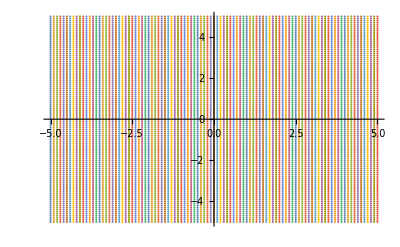

```mathematica
p1=ListPlot[lat]
```

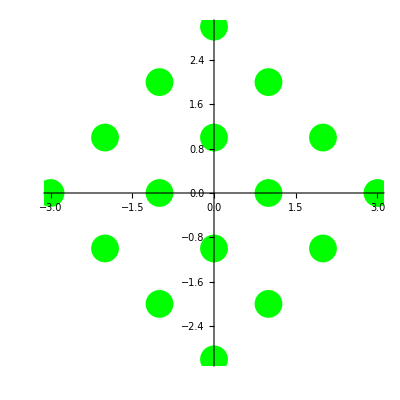

```mathematica
p2A=ListPlot[recA,PlotStyle->{PointSize->0.05,Green},AspectRatio->1]
```

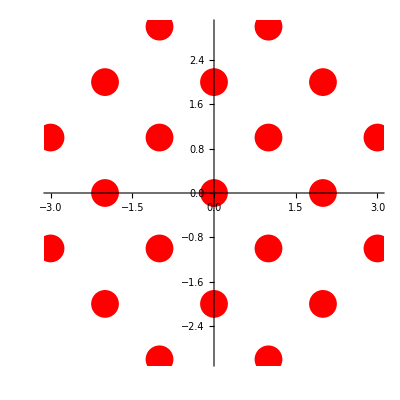

```mathematica
p2B=ListPlot[recB,PlotStyle->{PointSize->0.05,Red},AspectRatio->1]
```

```mathematica
pospos={}; (* coordinates of the probing points nearest to the nodes *)
```

```mathematica
Map[pospos={};AppendTo[pospos,lat[[#[[1]], #[[2]]]]]&, pos];
```

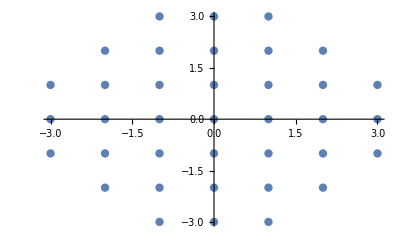

```mathematica
p4=ListPlot[pospos,PlotStyle->{PointSize->0.015}]
```

```mathematica
neighpospos={};
```

```mathematica
Map[neighpospos={};AppendTo[neighpospos,lat[[#[[1]], #[[2]]]]]&, Flatten[neighpos,1]];
```

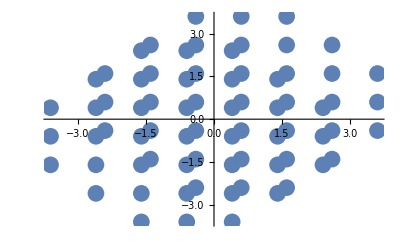

```mathematica
p5=ListPlot[neighpospos,PlotStyle->{PointSize->0.03}]
```

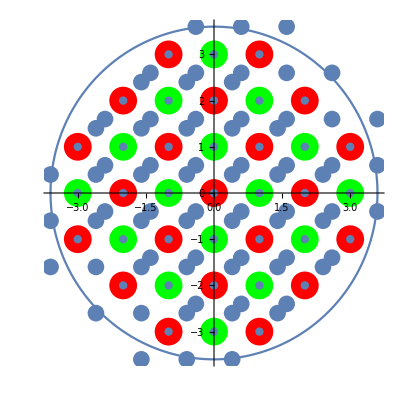

```mathematica
Show[ p2A,p2B,p4,p5,ParametricPlot[RTF{Cos[fi],Sin[fi]},{fi,0,2Pi}],PlotRange->All]
```

```mathematica
<<"wavefunction.m";
```

```mathematica
β=wannierNormalisationFactor[σw,δx,δy,lat];
```

```mathematica
(*Plot3D[wannier[{x,y},{0,0},σw,β],{x,-2σw,2σw},{y,-2σw,2σw}]*)
```

```mathematica
wavef=waveFunctionHarper[lat,a,J,J1,rec,RTF,k0,σw,β, δx, δy];
```

```mathematica
(*ListPlot3D[Abs@wavef]*)
```

```mathematica
(*ListDensityPlot[Table[{Flatten[lat,1][[i,1]],Flatten[lat,1][[i,2]],Abs@Flatten[wavef,1][[i]]},{i,Length[Flatten[lat,1]]}], AspectRatio->1,ColorFunction->"Rainbow",AxesLabel->{"x","y","|ψ|"},PlotRange->All]*)
```

```mathematica
FTwavef=Fourier[wavef];
```

```mathematica
(*ListPlot3D[Abs@mirror2DSpace[FTwavef],PlotRange->All,ColorFunction->"Rainbow"]*)
```

```mathematica
FTXAbs=Abs@Fourier[wavef];
```

```mathematica
wavefAbs=Abs@wavef;
```

```mathematica
support=Map[If[Norm[#]<RTF,1,0]&,lat,{2}];
```

```mathematica
<<"HIOER.m"
```

```mathematica
retr=phaseRetrieveGuess[FTXAbs,wavefAbs,support,nIterations,nRepeats,nHIO,gamma];
```

```mathematica
(*retr=phaseRetrieveSupport[FTXAbs,support,nIterations,nRepeats,nHIO,gamma];*)
```

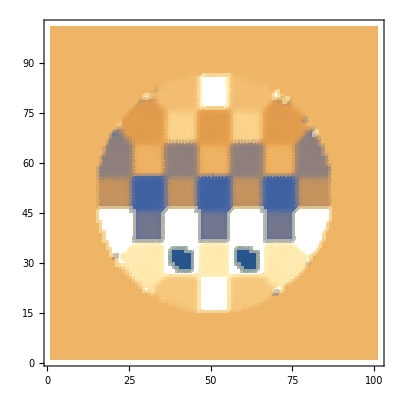

```mathematica
ListDensityPlot[Arg@retr]
```

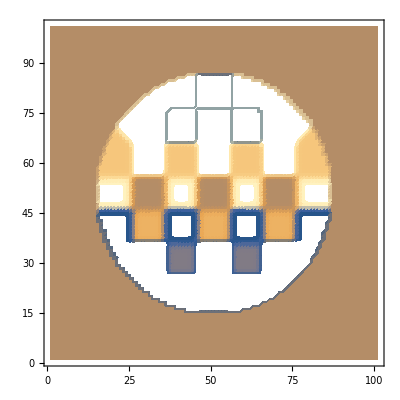

```mathematica
ListDensityPlot[Arg@wavef]
```

```mathematica
rec[[2]]
```

{{0.,-1.},-1.}

```mathematica
ξ=1/Sqrt[Total@Total@Map[If[Norm[RTF]>Norm[#],Norm[RTF]^2-Norm[#]^2,0]&,lat,{2}]*δx*δy]
```

0.798392

```mathematica
ckModel=wannierBaseRectProject[wavef,lat,rec,pos,neighpos,σw,β,δx,δy,RTF];
```

```mathematica
ckRetr=wannierBaseRectProject[retr,lat,rec,pos,neighpos,σw,β,δx,δy,RTF];
```

```mathematica
Total[Abs[ckRetr]^2]
```

1.

```mathematica
Abs[Conjugate[ckRetr].ckModel]^2
```

1.

```mathematica
guess[J_,J1_, ckModel_]:=Module[{
wavefJJ1 = waveFunctionHarper[lat,a,J,J1,rec,RTF,k0,σw,β, δx, δy]
},
1-Abs[Conjugate[wannierBaseRectProject[phaseRetrieveSupport[FTXAbs,Abs@wavefJJ1,support,nIterations,nRepeats,nHIO,gamma,RTF],lat,rec,pos,neighpos,σw,β,δx,δy,RTF]].ckModel]^2
]
```

```mathematica
(*guessT=ParallelTable[{J,J1,guess[J,J1,ckModel]},{J,0.33,2,0.33},{J1,0.33,2,0.33}, DistributedContexts->{"space`","wavefunction`","HIOER`"}]*)
```

```mathematica
(*ListPlot3D[Flatten[guessT,1]]*)
```

```mathematica
guess2[J_,J1_]:=Module[{
wavefJJ1 = waveFunctionHarper[lat,a,J,J1,rec,RTF,k0,σw,β, δx, δy]
},
wavefJJ1=phaseRetrieveSupport[FTXAbs,Abs@wavefJJ1,support,nIterations,nRepeats,nHIO,gamma]; (*nie ma nic wspolnego z wavefJJ1, jest to obiekt odzyskany w tej samej pamieci*)
Total@Total@Abs[Abs[Fourier[wavefJJ1]]^2-Abs[FTXAbs]^2]/Total[Total[Abs[FTXAbs]^2]] (*metryka bledu*)
]
```

```mathematica
(*guess2T=ParallelTable[{J1,guess2[J,J1]},{J1,0.1,3,0.3}, DistributedContexts->{"space`","wavefunction`","HIOER`"}]*)
```

```mathematica
(*ListPlot[guess2T,AxesLabel->{"J1/J","Niezgodnosc modulu tr. Fouriera zmierzonego z obliczonym z odzyskanej funkcji" } ]*)
```

```mathematica
(* find ckretr for kx,ky 2d table of 1st BZ*)
(* find Fxy for this set of ckretr*)
(* find chern number *)
```

```mathematica
<<"chernCalc.m"
```

```mathematica
BZ=latticeProbingPointsBZ[npts,a,q];
```

```mathematica
Dimensions@BZ
```

{5,5,2}

```mathematica
BZ
```

{{{0.628319,1.25664},{0.628319,2.51327},{0.628319,3.76991},{0.628319,5.02655},{0.628319,6.28319}},{{1.25664,1.25664},{1.25664,2.51327},{1.25664,3.76991},{1.25664,5.02655},{1.25664,6.28319}},{{1.88496,1.25664},{1.88496,2.51327},{1.88496,3.76991},{1.88496,5.02655},{1.88496,6.28319}},{{2.51327,1.25664},{2.51327,2.51327},{2.51327,3.76991},{2.51327,5.02655},{2.51327,6.28319}},{{3.14159,1.25664},{3.14159,2.51327},{3.14159,3.76991},{3.14159,5.02655},{3.14159,6.28319}}}

```mathematica
ckRetrBZ=ParallelMap[findCkRetr[#,J,J1,lat,a,rec,RTF,support,nIterations,nRepeats,nHIO,gamma,pos,neighpos,σw,β,δx,δy]&,BZ,{2}];
```

$Aborted

```mathematica
ckRetrBZ[[All,All,2]]
```

{{1.,0.999998,1.,0.999989,0.999999},{1.,0.999994,0.999993,1.,1.},{1.,1.,1.,0.999983,1.},{0.999993,0.999998,0.999998,1.,0.999999},{0.999997,0.999945,0.999954,0.999999,0.99996}}

```mathematica
FxyTRetr=FxyT[ckRetrBZ[[All, All,1]]]
```

{{-1.11022×10^-16+0.637725 ⅈ,3.08736×10^-17-0.00073117 ⅈ,0.-0.668717 ⅈ,-6.51063×10^-17-0.225576 ⅈ},{-2.22045×10^-16+1.73702 ⅈ,9.45297×10^-17+0.00758325 ⅈ,2.22045×10^-16-1.69877 ⅈ,-6.83047×10^-17-0.311978 ⅈ},{0.+0.633644 ⅈ,1.45852×10^-16+0.0150875 ⅈ,0.-0.646836 ⅈ,1.17636×10^-16-0.233882 ⅈ},{9.04225×10^-17+0.309912 ⅈ,-5.92398×10^-17-0.0910889 ⅈ,-7.43763×10^-17-0.326306 ⅈ,-6.04714×10^-17-0.151876 ⅈ}}

```mathematica
ckModelBZ=ParallelMap[findCkModel[#,J,J1,lat,a,rec,RTF,support,nIterations,nRepeats,nHIO,gamma,pos,neighpos,σw,β,δx,δy]&,BZ,{2}]
```

```mathematica
Dimensions@ckModelBZ
```

{5,5,37}

```mathematica
ckModelBZ2=ParallelMap[Activate,Flatten@Map[Inactivate[findCkModel[#,J,J1,lat,a,rec,RTF,support,nIterations,nRepeats,nHIO,gamma,pos,neighpos,σw,β,δx,δy]]&,BZ,{2}],DistributedContexts->All]
```

```mathematica
ckModelBZ3=ArrayReshape[ckModelBZ2,{First@Dimensions[BZ], Dimensions[BZ][[2]], Last@Dimensions[ckModelBZ2]}];
```

```mathematica
ckModelBZ3==ckModelBZ
```

True

```mathematica
Dimensions@ckModelBZ2
```

{25,37}

```mathematica
Dimensions@ckModelBZ
```

{3,3,37}

```mathematica
FxyTModel=FxyT[ckModelBZ]
```

{{-1.11022×10^-16+0. ⅈ,-1.94988×10^-17-0.026619 ⅈ},{2.46519×10^-32+2.22045×10^-16 ⅈ,1.13953×10^-16-0.00366158 ⅈ}}

```mathematica
{ListPlot3D[Abs[FxyTRetr],PlotRange->All],ListPlot3D[Abs[FxyTModel],PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
ListPlot3D[Abs[FxyTModel],PlotRange->All]
```

-Graphics3D-

```mathematica
w=1/(2π ⅈ )*Total@Total[FxyTRetr]//Chop
```

-0.16151

```mathematica
w=1/(2π ⅈ )*Total@Total[FxyTModel]//Chop
```

-0.00481931

```mathematica
t1=DateList[]
```

{2016,12,19,23,47,52.397596}

```mathematica
t2=DateList[]
```

{2016,12,19,23,47,52.554584}

```mathematica
ToString[t2-t1]
```

{0, 0, 0, 0, 0, 0.156988}

```mathematica
guess3[kGuess_]:=Module[{wavefkGuess=waveFunctionHarper[lat,a,J,J1,rec,RTF,kGuess,σw,β,δx,δy]},wavefkGuess=phaseRetrieveGuess[FTXAbs,Abs@wavefkGuess,support,nIterations,nRepeats,nHIO,gamma];(*nie ma nic wspolnego z wavefkGuess,jest to obiekt odzyskany w tej samej pamieci*)Total@Total@Abs[Abs[Fourier[wavefkGuess]]^2-Abs[FTXAbs]^2]/Total[Total[Abs[FTXAbs]^2]] (*metryka bledu*)]
```

```mathematica
guess3T=ParallelTable[{kxGuess,kyGuess,guess3[{kxGuess,kyGuess}]},{kxGuess,-2Pi/a,2Pi/a,0.3},{kyGuess,-2Pi/a,2Pi/a,0.3},DistributedContexts->{"space`","wavefunction`","HIOER`"}];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Dimensions@Flatten[guess3T,1]
```

{1764,3}

```mathematica
Flatten[guess3T,1]
```

{{-6.28319,-6.28319,0.814544},{-6.28319,-5.98319,0.981094},{-6.28319,-5.68319,1.08567},{-6.28319,-5.38319,1.09938},{-6.28319,-5.08319,0.931924},{-6.28319,-4.78319,0.787841},{-6.28319,-4.48319,1.06396},1751,{6.01681,4.51681,0.877032},{6.01681,4.81681,0.704982},{6.01681,5.11681,0.914178},{6.01681,5.41681,1.26072},{6.01681,5.71681,0.620038},{6.01681,6.01681,0.593195}}
 |  |  |  |

```mathematica
ListPointPlot3D[{{1,2,3},{4,5,6},{2,1,4}}]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[guess3T,1],AxesLabel->{"kx","ky", "1-error"},ColorFunction->Hue]
```

-Graphics3D-

```mathematica
kGuess=Import["/home/c8888/IdeaProjects/ChernRetrieval/out/kGuessData.dat","Table"];
```

```mathematica
Last@kGuess
```

{6.,5.7,0.0899529}

```mathematica
kGuess[[4]]
```

{0.,0.9,0.0848152}

```mathematica
ListPlot3D[kGuess,AxesLabel->{"kx","ky","error"}]
```

-Graphics3D-

```mathematica
tab={{1,1+I,3},{3,4+9I,2I}}
```

{{1,1+ⅈ,3},{3,4+9 ⅈ,2 ⅈ}}

```mathematica
Abs[tab] * Exp[I Arg[tab*1.]]
```

{{1,1.+1. ⅈ,3},{3,4.+9. ⅈ,1.22465×10^-16+2. ⅈ}}

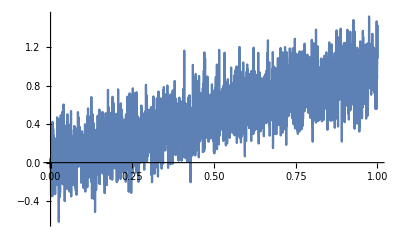

```mathematica
Plot[RandomVariate[NormalDistribution[x,0.01]],{x,0,1}]
```

```mathematica
RandomVa
```

```mathematica
σPhNoiseMin=0.001;
σPhNoiseMax=2;
σPhNoiseMult=2;
```

```mathematica
σPhNoise=Table[σPhNoiseMin*σPhNoiseMult^i,{i,0,Round@Log[σPhNoiseMax/σPhNoiseMin]/Log[σPhNoiseMult] }]
```

{0.001,0.002,0.004,0.008,0.016,0.032,0.064,0.128,0.256,0.512,1.024,2.048}

```mathematica
Transpose[{{1,2,3,4},{5,6,7,8}}]
```

{{1,5},{2,6},{3,7},{4,8}}

```mathematica
Map[RandomVariate[NormalDistribution[Arg[#],1]]&,wavef,{2}]
```

{{0.663519,0.218772,-1.92485,-0.451506,-1.32633,1.07883,-0.205749,-0.46895,85,0.326729,1.65539,-0.305751,1.51448,-1.65607,-0.99215,0.947598,-0.0720287},99,{1}}
 |  |  |  |

```mathematica
h={x,y,z}
```

{x,y,z}

```mathematica
i=N@CoordinateTransformData["Cartesian"->"Spherical","Mapping",h][[2;;3]]
```

{ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
{ArcCos[h[[3]]/Norm[h]],(*theta*)ArcTan[h[[1]],h[[2]]] (*phi*)}==i
```

{ArcCos[z/(√(Abs[x]^2+Abs[y]^2+Abs[z]^2))],ArcTan[x,y]}=={ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}